```mathematica
allDates =   {FromDateString["4/4/24"],FromDateString["4/11/24"],FromDateString["4/18/24"],FromDateString["4/25/24"],FromDateString["5/2/24"], FromDateString["5/09/24"], FromDateString["5/16/24"]}
```

{Thu 4 Apr 2024,Thu 11 Apr 2024,Thu 18 Apr 2024,Thu 25 Apr 2024,Thu 2 May 2024,Thu 9 May 2024,Thu 16 May 2024}

```mathematica
allDatesTues =  {FromDateString["4/2/24"],FromDateString["4/9/24"],FromDateString["4/16/24"],FromDateString["4/30/24"],FromDateString["5/7/24"], FromDateString["5/14/24"]}
```

{Tue 2 Apr 2024,Tue 9 Apr 2024,Tue 16 Apr 2024,Tue 30 Apr 2024,Tue 7 May 2024,Tue 14 May 2024}

```mathematica
updatedSched = SemanticImport["/Users/erichegonzales/Downloads/4v4 Schedule Adjuster - Tuesday Matchups Unchanged.csv"];
```

```mathematica
updatedSched
```

```mathematica
tableMatchups = Transpose[{Normal[Map[DateString, updatedSched[[All, "Date"]]]], Normal[updatedSched[[All, "Home Team"]]], Normal[updatedSched[[All, "Away Team"]]]}]
```

{{Tue 2 Apr 2024,Team 12 (Red Storm),Team 6 (Spartans)},{Tue 2 Apr 2024,Team 13 (Huskies),Team 5 (Wolfpack)},{Tue 2 Apr 2024,Team 1 (Cavaliers),Team 9 (Tar Heels)},{Tue 2 Apr 2024,Team 2 (Eagles),Team 3 (Tigers)},{Tue 2 Apr 2024,Team 14 (Bulldogs),Team 4 (Ducks)},{Tue 9 Apr 2024,Team 9 (Tar Heels),Team 7 (Wildcats)},{Tue 9 Apr 2024,Team 4 (Ducks),Team 12 (Red Storm)},{Tue 9 Apr 2024,Team 14 (Bulldogs),Team 8 (Hawks)},{Tue 9 Apr 2024,Team 3 (Tigers),Team 13 (Huskies)},{Tue 9 Apr 2024,Team 6 (Spartans),Team 10 (Gophers)},{Tue 9 Apr 2024,Team 5 (Wolfpack),Team 11 (Bears)},{Tue 9 Apr 2024,Team 2 (Eagles),Team 1 (Cavaliers)},{Tue 16 Apr 2024,Team 11 (Bears),Team 3 (Tigers)},{Tue 16 Apr 2024,Team 10 (Gophers),Team 4 (Ducks)},{Tue 16 Apr 2024,Team 13 (Huskies),Team 14 (Bulldogs)},{Tue 16 Apr 2024,Team 7 (Wildcats),Team 1 (Cavaliers)},{Tue 16 Apr 2024,Team 9 (Tar Heels),Team 5 (Wolfpack)},{Tue 16 Apr 2024,Team 12 (Red Storm),Team 2 (Eagles)},{Tue 16 Apr 2024,Team 8 (Hawks),Team 6 (Spartans)},{Tue 30 Apr 2024,Team 3 (Tigers),Team 14 (Bulldogs)},{Tue 30 Apr 2024,Team 6 (Spartans),Team 4 (Ducks)},{Tue 30 Apr 2024,Team 8 (Hawks),Team 2 (Eagles)},{Tue 30 Apr 2024,Team 5 (Wolfpack),Team 1 (Cavaliers)},{Tue 30 Apr 2024,Team 10 (Gophers),Team 13 (Huskies)},{Tue 7 May 2024,Team 6 (Spartans),Team 2 (Eagles)},{Tue 7 May 2024,Team 14 (Bulldogs),Team 7 (Wildcats)},{Tue 7 May 2024,Team 1 (Cavaliers),Team 4 (Ducks)},{Tue 7 May 2024,Team 10 (Gophers),Team 11 (Bears)},{Tue 7 May 2024,Team 13 (Huskies),Team 8 (Hawks)},{Tue 7 May 2024,Team 9 (Tar Heels),Team 12 (Red Storm)},{Tue 7 May 2024,Team 5 (Wolfpack),Team 3 (Tigers)},{Tue 14 May 2024,Team 7 (Wildcats),Team 12 (Red Storm)},{Tue 14 May 2024,Team 8 (Hawks),Team 13 (Huskies)},{Tue 14 May 2024,Team 9 (Tar Heels),Team 10 (Gophers)},{Tue 14 May 2024,Team 3 (Tigers),Team 1 (Cavaliers)},{Tue 14 May 2024,Team 4 (Ducks),Team 2 (Eagles)},{Tue 14 May 2024,Team 5 (Wolfpack),Team 14 (Bulldogs)},{Tue 14 May 2024,Team 6 (Spartans),Team 11 (Bears)}}

```mathematica
getEdges[matchups_]:= MapApply[#2<->#3&, matchups]
```

```mathematica
Length[tableMatchups]
```

38

```mathematica
{513, 538, 562, 587, }
```

```mathematica
TableView[tableMatchups, ItemSize->{15, 1}]
```

```mathematica
Normal[%72]
```

```mathematica
byWeek = updatedSched[GroupBy["Date"]]
```

```mathematica
week25 = Normal[byWeek][FromDateString["4/25/24"]]
```

```mathematica
weekEdges = #["Home Team"]<->#["Away Team"]&/@ week25
```

week25

```mathematica
allteams = Union[Normal[Join[updatedSched[[All, "Home Team"]], updatedSched[[All, "Away Team"]]]]]
```

{Team 10 (Gophers),Team 11 (Bears),Team 12 (Red Storm),Team 13 (Huskies),Team 14 (Bulldogs),Team 1 (Cavaliers),Team 2 (Eagles),Team 3 (Tigers),Team 4 (Ducks),Team 5 (Wolfpack),Team 6 (Spartans),Team 7 (Wildcats),Team 8 (Hawks),Team 9 (Tar Heels)}

```mathematica
weekteams = Union[Join[week25[[All, "Home Team"]], week25[[All, "Away Team"]]]]
```

```mathematica
edges =Normal[ #["Home Team"]<->#["Away Team"]&/@ updatedSched]
```

{Team 12 (Red Storm)<->Team 6 (Spartans),Team 13 (Huskies)<->Team 5 (Wolfpack),Team 1 (Cavaliers)<->Team 9 (Tar Heels),Team 2 (Eagles)<->Team 3 (Tigers),Team 14 (Bulldogs)<->Team 4 (Ducks),Team 9 (Tar Heels)<->Team 7 (Wildcats),Team 4 (Ducks)<->Team 12 (Red Storm),Team 14 (Bulldogs)<->Team 8 (Hawks),Team 3 (Tigers)<->Team 13 (Huskies),Team 6 (Spartans)<->Team 10 (Gophers),Team 5 (Wolfpack)<->Team 11 (Bears),Team 2 (Eagles)<->Team 1 (Cavaliers),Team 11 (Bears)<->Team 3 (Tigers),Team 10 (Gophers)<->Team 4 (Ducks),Team 13 (Huskies)<->Team 14 (Bulldogs),Team 7 (Wildcats)<->Team 1 (Cavaliers),Team 9 (Tar Heels)<->Team 5 (Wolfpack),Team 12 (Red Storm)<->Team 2 (Eagles),Team 8 (Hawks)<->Team 6 (Spartans),Team 3 (Tigers)<->Team 14 (Bulldogs),Team 6 (Spartans)<->Team 4 (Ducks),Team 8 (Hawks)<->Team 2 (Eagles),Team 5 (Wolfpack)<->Team 1 (Cavaliers),Team 10 (Gophers)<->Team 13 (Huskies),Team 6 (Spartans)<->Team 2 (Eagles),Team 14 (Bulldogs)<->Team 7 (Wildcats),Team 1 (Cavaliers)<->Team 4 (Ducks),Team 10 (Gophers)<->Team 11 (Bears),Team 13 (Huskies)<->Team 8 (Hawks),Team 9 (Tar Heels)<->Team 12 (Red Storm),Team 5 (Wolfpack)<->Team 3 (Tigers),Team 7 (Wildcats)<->Team 12 (Red Storm),Team 8 (Hawks)<->Team 13 (Huskies),Team 9 (Tar Heels)<->Team 10 (Gophers),Team 3 (Tigers)<->Team 1 (Cavaliers),Team 4 (Ducks)<->Team 2 (Eagles),Team 5 (Wolfpack)<->Team 14 (Bulldogs),Team 6 (Spartans)<->Team 11 (Bears)}

```mathematica
Length[edges]
```

38

```mathematica
getStyle[teams_]:= If[divsTues[#] == "West", #-> Red, If[divsTues[#] == "East", #-> Green, If[divsTues[#] == "West/East", #-> Yellow]]]& /@ teams
```

```mathematica
divs = <|"Team 10 (Tar Heels)"->"West","Team 11 (Cavaliers)"->"West/East","Team 12 (Ducks)"->"East","Team 13 (Bears)"->"East","Team 14 (Hawks)"->"West","Team 1 (Gophers)"->"West","Team 2 (Tigers)"->"East","Team 3 (Spartans)"->"West","Team 4 (Wolfpack)"->"West/East","Team 5 (Bulldogs)"->"West","Team 6 (Wildcats)"->"West","Team 7 (Red Storm)"->"East","Team 8 (Eagles)"->"East","Team 9 (Huskies)"->"East"|>
```

<|Team 10 (Tar Heels)→West,Team 11 (Cavaliers)→West/East,Team 12 (Ducks)→East,Team 13 (Bears)→East,Team 14 (Hawks)→West,Team 1 (Gophers)→West,Team 2 (Tigers)→East,Team 3 (Spartans)→West,Team 4 (Wolfpack)→West/East,Team 5 (Bulldogs)→West,Team 6 (Wildcats)→West,Team 7 (Red Storm)→East,Team 8 (Eagles)→East,Team 9 (Huskies)→East|>

```mathematica
divsTues = <|"Team 10 (Gophers)"->"West","Team 11 (Bears)"->"East","Team 12 (Red Storm)"->"East","Team 13 (Huskies)"->"West","Team 14 (Bulldogs)"->"East","Team 1 (Cavaliers)"->"West","Team 2 (Eagles)"->"West","Team 3 (Tigers)"->"West","Team 4 (Ducks)"->"West","Team 5 (Wolfpack)"->"East","Team 6 (Spartans)"->"East","Team 7 (Wildcats)"->"East","Team 8 (Hawks)"->"West","Team 9 (Tar Heels)"->"West"|>
```

<|Team 10 (Gophers)→West,Team 11 (Bears)→East,Team 12 (Red Storm)→East,Team 13 (Huskies)→West,Team 14 (Bulldogs)→East,Team 1 (Cavaliers)→West,Team 2 (Eagles)→West,Team 3 (Tigers)→West,Team 4 (Ducks)→West,Team 5 (Wolfpack)→East,Team 6 (Spartans)→East,Team 7 (Wildcats)→East,Team 8 (Hawks)→West,Team 9 (Tar Heels)→West|>

```mathematica
eastTeams = Select[divs, #== "East"&]
westTeams = Select[divs, #== "West"&]
centTeams = Select[divs, #== "East/West"||#=="West/East"&]
```

<|Team 12 (Ducks)→East,Team 13 (Bears)→East,Team 2 (Tigers)→East,Team 7 (Red Storm)→East,Team 8 (Eagles)→East,Team 9 (Huskies)→East|>

<|Team 10 (Tar Heels)→West,Team 14 (Hawks)→West,Team 1 (Gophers)→West,Team 3 (Spartans)→West,Team 5 (Bulldogs)→West,Team 6 (Wildcats)→West|>

<|Team 11 (Cavaliers)→West/East,Team 4 (Wolfpack)→West/East|>

```mathematica
updatedG = Graph[edges, VertexStyle->getStyle[allteams], VertexLabels->"Name"]
```

-Graphics-

```mathematica
coords =  GraphEmbedding[updatedG]
```

{{0.346045,1.54744},{1.65755,2.03781},{2.48366,0.450069},{1.66504,0.},{0.842346,0.714089},{0.593408,0.322352},{1.33334,1.57698},{1.90664,0.482054},{1.40119,0.741403},{0.892346,1.73609},{0.,0.671305},{2.35874,1.62761},{1.7442,1.17469},{2.51891,1.01653}}

```mathematica
Manipulate[Module[{weekMatchups, weekEdges, weekGraph, listWeekMatchups},
weekMatchups = Normal[byWeek][DateString[week]];
weekEdges = #["Home Team"]<->#["Away Team"]&/@ weekMatchups;
listWeekMatchups = Transpose[{weekMatchups[[All, "Home Team"]], weekMatchups[[All, "Away Team"]]}];
Column[{weekGraph = Graph[getEdges[tableMatchups], VertexStyle->getStyle[allteams], VertexLabels->"Name", GraphHighlight->weekEdges, GraphHighlightStyle->"Thick", ImageSize->Large],
TableView[Dynamic[tableMatchups], ItemSize->{15, 1}]}]],
{week,allDates}, ControlType->SetterBar]
```

```mathematica
tableMatchupsByWeek = GroupBy[tableMatchups, #[[1]]&]
```

```mathematica
DateString[DateObject[{2024,4,4},"Day"]]
```

Thu 4 Apr 2024

```mathematica
getEdges[tableMatchupsByWeek[DateString[DateObject[{2024,4,4},"Day"]]]]
```

```mathematica
Manipulate[Module[{tableMatchupsByWeek, weekMatchups, weekEdges, weekGraph, listWeekMatchups},
tableMatchupsByWeek = GroupBy[tableMatchups, #[[1]]&];
weekMatchups = tableMatchupsByWeek[DateString[week]];
weekEdges = getEdges[weekMatchups];
Column[{weekGraph = Graph[getEdges[tableMatchups], VertexStyle->getStyle[allteams], VertexLabels->"Name", GraphHighlight->weekEdges, GraphHighlightStyle->"Thick",ImageSize->Large, VertexCoordinates -> currCoords], 
TableView[Dynamic[tableMatchups], ItemSize->{15, 1}]}]],
{week,allDatesTues}, ControlType->SetterBar]
```

GroupBy::list1: The argument tableMatchups is not a valid list of Associations or rules or lists of rules.

GroupBy::argx: GroupBy called with 2 arguments; 1 argument is expected.

Part::partw: Part 2 of GroupBy[tableMatchups,#1⟦1⟧&][Tue 7 May 2024] does not exist.

Part::pkspec1: The expression Tue 7 May 2024→2 cannot be used as a part specification.

Part::partd: Part specification tableMatchups⟦2⟧ is longer than depth of object.

Part::partd: Part specification tableMatchups⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression tableMatchups⟦1⟧→2 cannot be used as a part specification.

GroupBy::list1: The argument Null is not a valid list of Associations or rules or lists of rules.

GroupBy::argx: GroupBy called with 2 arguments; 1 argument is expected.

Part::partw: Part 2 of GroupBy[Null,#1⟦1⟧&][Tue 7 May 2024] does not exist.

Part::pkspec1: The expression Tue 7 May 2024→2 cannot be used as a part specification.

Part::partd: Part specification Null⟦2⟧ is longer than depth of object.

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression Null⟦1⟧→2 cannot be used as a part specification.

GroupBy::list1: 
   The argument tableMatchups is not a valid list of Associations or rules or
     lists of rules.

GroupBy::argx: GroupBy called with 2 arguments; 1 argument is expected.

GroupBy::list1: The argument Null is not a valid list of Associations or rules or lists of rules.

GroupBy::argx: GroupBy called with 2 arguments; 1 argument is expected.

Part::partw: Part 2 of GroupBy[Null,#1⟦1⟧&][Tue 2 Apr 2024] does not exist.

Part::pkspec1: The expression Tue 2 Apr 2024→2 cannot be used as a part specification.

Part::partd: Part specification Null⟦2⟧ is longer than depth of object.

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression Null⟦1⟧→2 cannot be used as a part specification.

GroupBy::list1: The argument Null is not a valid list of Associations or rules or lists of rules.

GroupBy::argx: GroupBy called with 2 arguments; 1 argument is expected.

Part::partw: Part 2 of GroupBy[Null,#1⟦1⟧&][Tue 2 Apr 2024] does not exist.

Part::pkspec1: The expression Tue 2 Apr 2024→2 cannot be used as a part specification.

Part::partd: Part specification Null⟦2⟧ is longer than depth of object.

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression Null⟦1⟧→2 cannot be used as a part specification.

GroupBy::list1: 
   The argument tableMatchups is not a valid list of Associations or rules or
     lists of rules.

GroupBy::argx: GroupBy called with 2 arguments; 1 argument is expected.

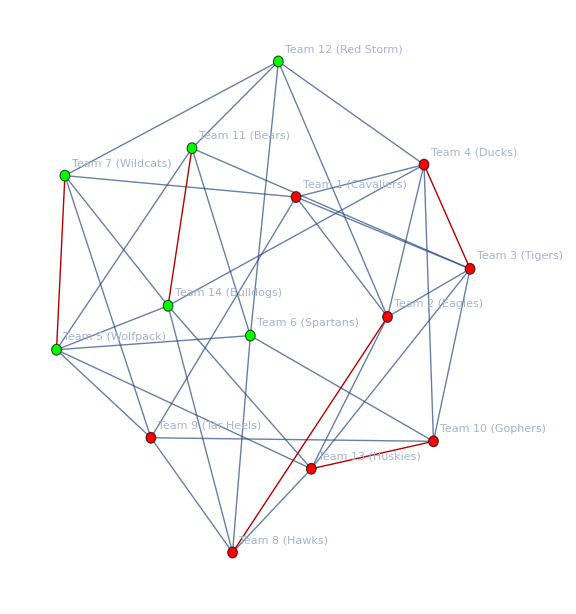
```mathematica
currCoords = GraphEmbedding[-Graphics-]
```

{{1.10629,2.20233},{0.966692,0.972821},{1.27071,0.375501},{0.,0.90947},{1.19467,1.59444},{0.470787,0.514603},{1.65085,1.05677},{2.06268,1.27229},{0.556333,1.10659},{1.83306,1.73964},{0.041785,1.69038},{0.877947,0.},{1.88006,0.498622},{0.675507,1.81339}}

```mathematica
Export["Projects/Wolfram/TuesdaySchedule424.csv", tableMatchups]
```

Projects/Wolfram/TuesdaySchedule424.csv